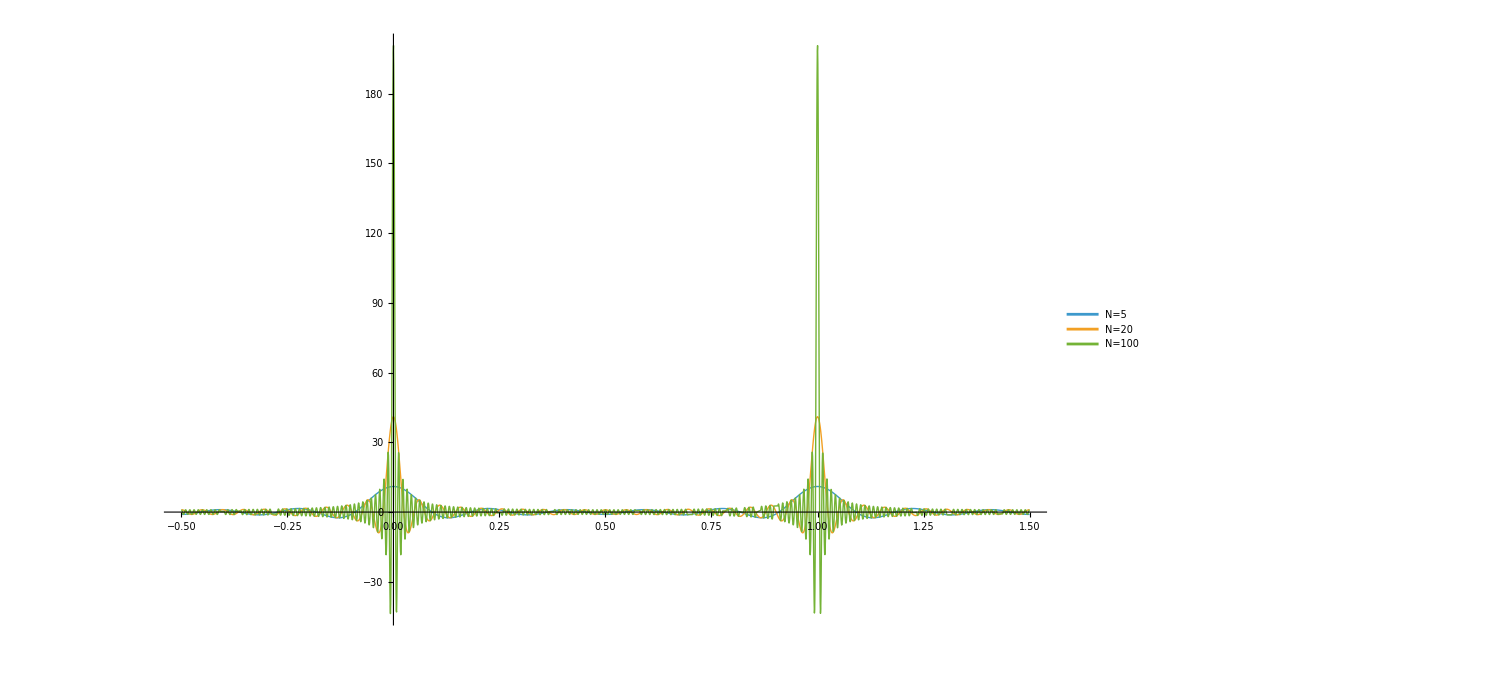

```mathematica
(*定义部分和函数*)diracApprox[t_,T_,N_]:=(1/T)*Sum[Cos[k*(2 Pi/T)*t],{k,-N,N}]

(*绘制随着项数 N 增加的效果*)
Plot[Table[diracApprox[t,1,n],{n,{5,20,100}}]//Evaluate,{t,-0.5,1.5},PlotRange->All,PlotLegends->{"N=5","N=20","N=100"},PlotStyle->Thick]
```

```mathematica
(*定义 T 为采样周期*)T=1;

Manipulate[Plot[(*右侧级数的第 k 项是 (1/T)*Exp[j k (2Pi/T) t]*)(*对称求和后，复指数项合并为 Cos 项*)(1/T)*(1+2*Sum[Cos[k*(2*Pi/T)*t],{k,1,N}]),{t,-0.5,2.5},PlotRange->{-2,2*N/T+1},(*动态调整纵坐标以适应尖峰*)Filling->Axis,PlotStyle->{Thick,Orange},AxesLabel->{"t","x(t)"},PlotLabel->Style["傅里叶级数合成狄拉克梳状函数 (N = "<>ToString[N]<>")",15,Bold],Exclusions->None],{{N,1,"累加项数 (N)"},1,100,1,Appearance->"Labeled"}]
```

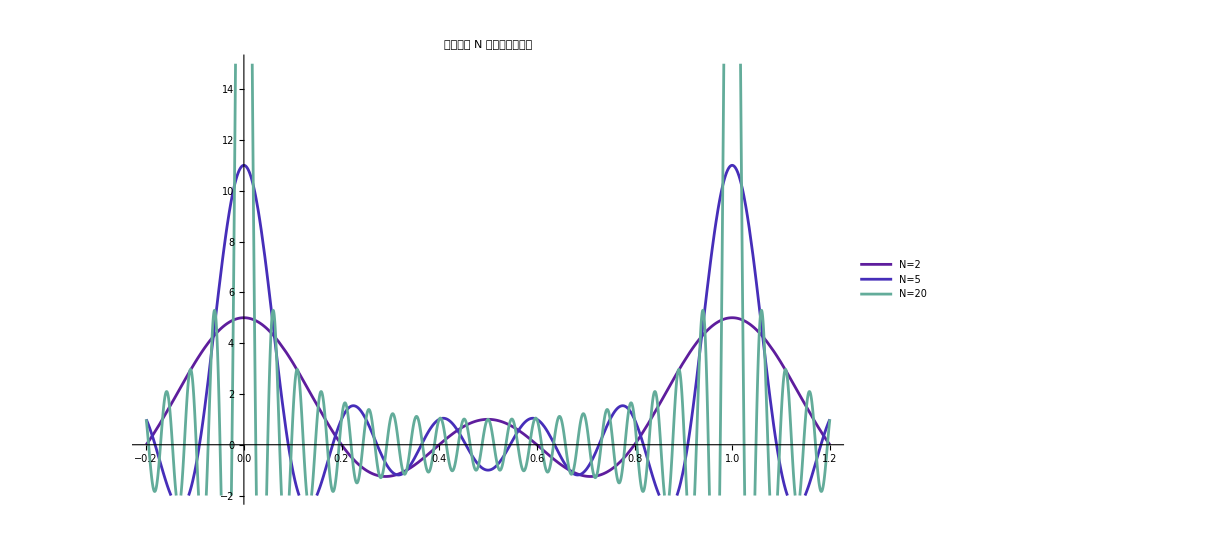

```mathematica
T=1;
plots=Table[Plot[(1/T)*(1+2*Sum[Cos[k*(2*Pi/T)*t],{k,1,n}]),{t,-0.2,1.2},PlotRange->{-2,15},PlotStyle->ColorData["Rainbow"][n/50],PlotLegends->{"N="<>ToString[n]}],{n,{2,5,20}}];

Show[plots,PlotLabel->"不同项数 N 的逼近效果对比"]
```

```mathematica
T=1;
Manipulate[Plot[(1/T)*(1+2*Sum[Cos[k*(2*Pi/T)*t],{k,1,N}]),{t,-0.5,2.5},(*关键改进 1：增加采样点，确保能抓到窄脉冲*)PlotPoints->500,(*关键改进 2：告诉绘图引擎在整数周期处有特殊情况*)Exclusions->{0,1,2},PlotRange->{-2,2*N/T+2},Filling->Axis,PlotStyle->{Thick,Orange},AxesLabel->{"t","x(t)"},PlotLabel->Style["N = "<>ToString[N]<>" 时的同步相长干涉",14]],{{N,1,"项数"},1,200,1,Appearance->"Labeled"}]
```